```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## curvature, osculating circle, evolute

#### Osculating Circle

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,6},{1.5,5.1},PlotOsculatingCircle->True,PlotParameterValue->True,PlotEvolute->True]
```

-Graphics-

#### (* Equiangular Spiral with it's increasing curvature *)

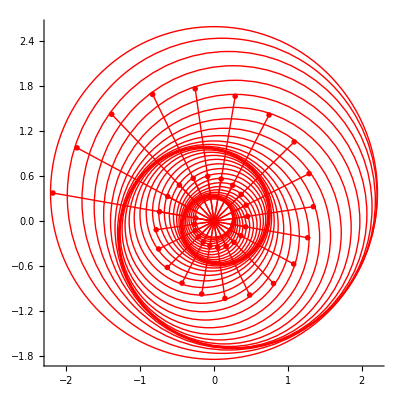

```mathematica
PlaneCurvePlot[{1/4 ⅇ^(t Cot[1.4]) Cos[t],1/4 ⅇ^(t Cot[1.4]) Sin[t]},{t,0,4 π,(4 π)/40},PlotOsculatingCircle->True,LineStyle->{Hue[0]},PlotRadial->True,PlotCurve->False,PlotDot->False]
```

#### (* Hypotrochoid osculating beauty, [1,3/8,.1] *)

```mathematica
PlaneCurvePlot[{(5 Cos[t])/8+0.1 Cos[(5 t)/3],(5 Sin[t])/8-0.1 Sin[(5 t)/3]},{t,0,3 2 π,(6 π)/32},PlotDot->False,PlotOsculatingCircle->True,CurveColorFunction->{Hue},CurveStyle->{Thickness[.015]},PlotRange->{{-2,2},{-2,2}},Background->Black]
```

-Graphics-

#### (* Hypotrochoid osculating beauty, [1,3/7,3/7] *)

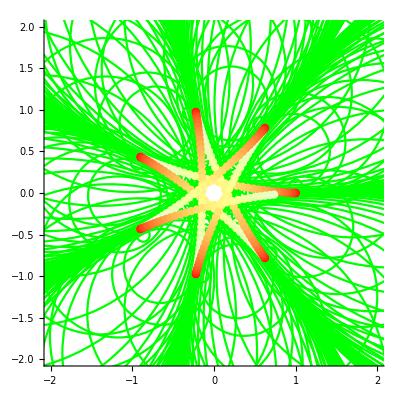

```mathematica
PlaneCurvePlot[{(4 Cos[t])/7+3/7 Cos[(4 t)/3],(4 Sin[t])/7-3/7 Sin[(4 t)/3]},{t,0.01,18.22,(3 2 π)/(7 41)},DotStyle->Table[{PointSize[.015],Hue[i,3.33 (.3-i),1]},{i,0,.3,(.3)/40}],PlotOsculatingCircle->True,PlotCurve->False,PlotRange->{{-2,2},{-2,2}}]
```

#### (* Hypotrochoid osculating beauty, [1,3/7,1] *)

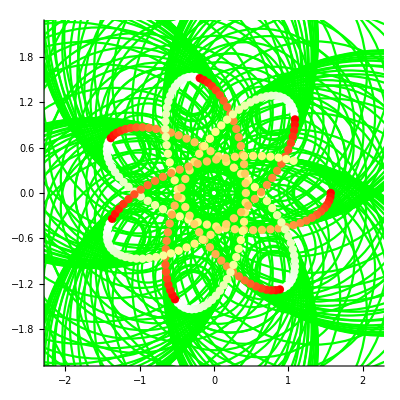

```mathematica
PlaneCurvePlot[{(4 Cos[t])/7+Cos[(4 t)/3],(4 Sin[t])/7-Sin[(4 t)/3]},{t,0,18.22,(3 2 π)/(7 40)},DotStyle->Table[{PointSize[.015],Hue[i,3.33 (.3-i),1]},{i,0,.3,(.3)/40}],PlotOsculatingCircle->True,PlotCurve->False,PlotRange->{{-2.2,2.2},{-2.2,2.2}}]
```

### Evolute

#### (* Illustration for understanding evolute and osculating circles *)

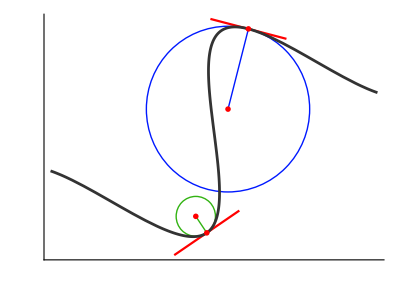

```mathematica
PlaneCurvePlot[{0.8+t Cos[34 °]-Sin[34 °] Sin[2 t],0.8+t Sin[34 °]+Cos[34 °] Sin[2 t]},{t,-2,2},{π/4+.3,-π/4},PlotEvolute->True,PlotOsculatingCircle->True,TangentLineLength->1,LineStyle->{{Hue[.65]},{Hue[.3,.9,.7]}},CurveColorFunction->{GrayLevel[.2]&},PlotRange->All,Ticks->None]
```

#### (* The evolute of a cycloid is another cycloid *)

```mathematica
PlaneCurvePlot[{t-Sin[t],1-Cos[t]},{t,0,2 2 π,(2 2 π)/60},PlotEvolute->True,LineStyle->{Hue[.43]}]
```

-Graphics-

#### (* The evolute of tracktrix is catenary *)

```mathematica
PlaneCurvePlot[{Log[Sec[t]+Tan[t]]-Sin[t],Cos[t]},{t,-1.53,1.53,.1},PlotEvolute->True,PlotRange->{{-3,3},{0,3}}]
```

-Graphics-

#### (* The evolute of astroid is another astroid *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/80},PlotEvolute->True,LineStyle->{Hue[0]},DotStyle->{Hue[.8]},Axes->False]
```

-Graphics-

#### (* 8 leaved rose and its evolute *)

```mathematica
PlaneCurvePlot[{Cos[4 t] Cos[t],Cos[4 t] Sin[t]},{t,0,2 π,(2 π)/120},PlotEvolute->True,LineStyle->{Hue[.43]}]
```

-Graphics-

## Radial

#### (* Parabola and its Radial *)

```mathematica
PlaneCurvePlot[{Cos[t],2 Sin[t]},{t,0,2 π,(2 π)/60},PlotRadial->True,PlotCurve->True,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Radial of a cycloid is a circle *)

```mathematica
PlaneCurvePlot[{t-Sin[t],1-Cos[t]},{t,0,2 2 π,(2 2 π)/60},PlotRadial->True,LineStyle->{Hue[.43]},AspectRatio->Automatic]
```

-Graphics-

#### (* Radial of a catenary is Kampyle of Eudoxus *)

```mathematica
PlaneCurvePlot[{t,Cosh[t]},{t,-2,2,.15},PlotRadial->True,AspectRatio->Automatic,PlotRange->{{-10,10},{-1,4}}]
```

-Graphics-

#### (* Radial of astroid is a 4 leaved rose *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/100},PlotRadial->True,PlotDot->False,LineStyle->{Hue[0]},DotStyle->{{Hue[.9],PointSize[.01]}},AspectRatio->Automatic,Axes->False]
```

-Graphics-

#### (* Radial of Rose (a hypotrochoid) is another hypotrochoid *)

```mathematica
PlaneCurvePlot[{Cos[3 t] Cos[t],Cos[3 t] Sin[t]},{t,0,π,π/120},PlotRadial->True,PlotDot->False,LineStyle->{Hue[0]},AspectRatio->Automatic]
```

-Graphics-